## Naloga 1 (Polžek)

[20 točk] Sestavite funkcijo polzek[l_], kot je zapisano v navodilih.

```mathematica
ClearAll[polzek]
polzek[l_]:=With[{n=Ceiling[Sqrt[Length[l]]]},
With[{ll=l~Join~Table[0,{i,n^2-Length[l]}]},
If[n≤2,
If[n==1,{{First[ll]}},{ll[[1;;2]],Reverse[ll[[3;;4]]]}],
{ll[[;;n]]}~Join~
Transpose[
{Reverse[ll[[3n-1;;4n-4]]]}~Join~
Transpose[polzek[ll[[4n-3;;]]]]~Join~
{ll[[n+1;;2n-2]]}
]~Join~
{Reverse[ll[[2n-1;;3n-2]]]}
]
]]
```

```mathematica
polzek[{1,4,-1,-3,2}]//MatrixForm
```

(1 | 4 | -1
0 | 0 | -3
0 | 0 | 2)

```mathematica
polzek[{2,3,5,7,11,13,17,19,23,29,2,7}]//MatrixForm
```

(2 | 3 | 5 | 7
7 | 0 | 0 | 11
2 | 0 | 0 | 13
29 | 23 | 19 | 17)

```mathematica
polzek[{4,3,2,1}]//MatrixForm
```

(4 | 3
1 | 2)

```mathematica
polzek[{13}]//MatrixForm
```

(13)

[10 točk] Sestavite funkcijo odvij[l_], kot je zapisano v navodilih.

```mathematica
ClearAll[odvij]
odvij[m_]/;Length[m]==1:=First[m]
odvij[m_]:=With[{
n=Length[m],
p=First[m],
z=Last[m],
vmes=Rest[Most[m]]
},
If[n==2,
p~Join~Reverse[z],
p~Join~Last[Transpose[vmes]]~Join~
Reverse[z]~Join~Reverse[First[Transpose[vmes]]]~Join~odvij[Transpose[Rest[Most[Transpose[vmes]]]]]
]
]
```

```mathematica
odvij[{{1,4,-1},{0,0,-3},{0,0,2}}]
```

{1,4,-1,-3,2,0,0,0,0}

```mathematica
odvij[{{2,3,5,7},{7,0,0,11},{2,0,0,13},{29,23,19,17}}]
```

{2,3,5,7,11,13,17,19,23,29,2,7,0,0,0,0}

```mathematica
odvij[{{4,3},{1,2}}]
```

{4,3,2,1}

```mathematica
odvij[{{13}}]
```

{13}

## Naloga 2 (Šestkotniki)

[30 točk] Sestavite funkcijo benz[l_], kot je zapisano v navodilih.

```mathematica
PolarToCartesian[{r_,fi_}]:={r*Cos[fi],r*Sin[fi]}
hex[{u_,v_}]:=With[{x=Sqrt[3]*(u+v/2),y=3v/2},
({{x,y},{x,y}}+#&)/@Table[{PolarToCartesian[{1,Pi/6+Pi*i/3}],PolarToCartesian[{1,3*Pi/6+Pi*i/3}]},{i,0,5}]
]
benz[l_]:=Graphics[Line/@Join@@(hex/@l)]
```

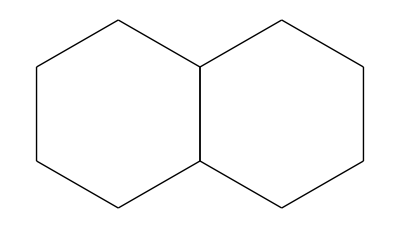

```mathematica
benz[{{-1,0},{0,0}}]
```

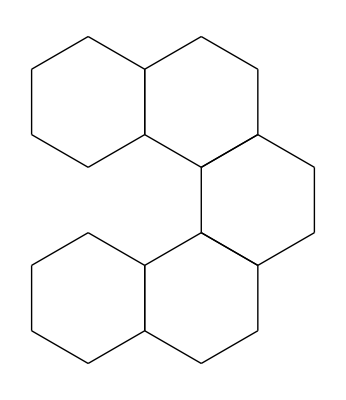

```mathematica
benz[{{0,0},{1,0},{1,1},{0,2},{-1,2}}]
```